```mathematica
midiIn={77,84,104,100,0,0,0,6,0,0,0,1,0,96,77,84,114,107,0,0,0,255,0,255,3,7,66,76,95,52,95,67,0,0,255,88,4,4,2,36,8,0,255,88,4,4,2,36,8,0,144,60,95,36,128,60,32,13,144,36,95,11,128,36,32,13,144,48,95,10,128,48,32,13,144,48,127,13,128,48,32,11,144,60,95,13,128,60,32,13,144,48,95,10,128,48,32,12,144,72,95,25,144,48,95,9,128,72,32,27,128,48,32,11,144,48,127,13,128,48,32,11,144,48,95,12,128,48,32,12,144,60,95,12,128,60,32,13,144,48,127,10,128,48,32,13,144,48,127,11,128,48,32,13,144,48,95,13,128,48,32,11,144,60,95,37,128,60,32,12,144,36,95,11,128,36,32,13,144,48,95,12,128,48,32,11,144,48,127,13,128,48,32,11,144,60,95,12,128,60,32,13,144,48,95,11,128,48,32,11,144,72,95,26,144,48,95,9,128,72,32,26,128,48,32,12,144,48,127,13,128,48,32,10,144,48,95,13,128,48,32,12,144,60,95,12,128,60,32,13,144,48,127,10,128,48,32,14,144,48,127,10,128,48,32,13,144,48,95,13,128,48,32,0,255,47,0};
```

```mathematica
tracknumber=1
```

1

```mathematica
Length[midiIn]/tracknumber
```

277

```mathematica
ch=1;(*assuming a range of 1-16*)
noteonPos=Position[midiIn,143+ch];

noteoffPos=Position[midiIn,127+ch];

timeEvents=Flatten[Union[noteonPos,noteoffPos]-1];(*These are timing events since the last timing event.*)realTimeEvents=Accumulate[midiIn[[timeEvents]]];(*Time events are accumulated to give actual timing events.*)midi=ReplacePart[midiIn,Table[timeEvents[[i]]->realTimeEvents[[i]],{i,Length[timeEvents]}]];(*The original timing events are replaced by the real timing events*)extractEvents[data_List,{x_}]:=Extract[data,{{x-1},{x},{x+1},{x+2}}];(*This function is for extracting timing,note event,note number,and velocity for each note on/off evnt*)noteOn=Flatten[{#,extractEvents[midi,#]}]&/@noteonPos;(*This extracts each note on event and prepends with the events position in the imported list*)noteOff=Flatten[{#,extractEvents[midi,#]}]&/@noteoffPos;(*This extracts each note off event and prepends with the events position in the imported list*)
```

```mathematica
notes=Table[{noteOn[[i]],First[Select[noteOff,#[[1]]>noteOn[[i,1]]&&#[[4]]==noteOn[[i,4]]&]]},{i,Length[noteOn]}](*Pair the correct note off messages with each note on message*)
```

{{{51,0,144,60,95},{55,36,128,60,32}},{{59,49,144,36,95},{63,60,128,36,32}},{{67,73,144,48,95},{71,83,128,48,32}},{{75,96,144,48,127},{79,109,128,48,32}},{{83,120,144,60,95},{87,133,128,60,32}},{{91,146,144,48,95},{95,156,128,48,32}},{{99,168,144,72,95},{107,202,128,72,32}},{{103,193,144,48,95},{111,229,128,48,32}},{{115,240,144,48,127},{119,253,128,48,32}},{{123,264,144,48,95},{127,276,128,48,32}},{{131,288,144,60,95},{135,300,128,60,32}},{{139,313,144,48,127},{143,323,128,48,32}},{{147,336,144,48,127},{151,347,128,48,32}},{{155,360,144,48,95},{159,373,128,48,32}},{{163,384,144,60,95},{167,421,128,60,32}},{{171,433,144,36,95},{175,444,128,36,32}},{{179,457,144,48,95},{183,469,128,48,32}},{{187,480,144,48,127},{191,493,128,48,32}},{{195,504,144,60,95},{199,516,128,60,32}},{{203,529,144,48,95},{207,540,128,48,32}},{{211,551,144,72,95},{219,586,128,72,32}},{{215,577,144,48,95},{223,612,128,48,32}},{{227,624,144,48,127},{231,637,128,48,32}},{{235,647,144,48,95},{239,660,128,48,32}},{{243,672,144,60,95},{247,684,128,60,32}},{{251,697,144,48,127},{255,707,128,48,32}},{{259,721,144,48,127},{263,731,128,48,32}},{{267,744,144,48,95},{271,757,128,48,32}}}

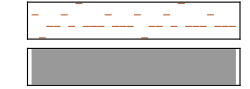

```mathematica
g=Sound[Table[SoundNote[notes[[n]][[1]][[4]]-60,0.2,"JazzGuitar"],{n,1,Length[notes]}]]
```

```mathematica
Export["MarkH_HisMelody.mid", g]
```

MarkH_HisMelody.mid

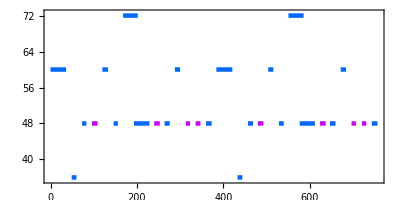

```mathematica
Graphics[{Hue[0.8#[[1,5]]/127],Rectangle[#[[1,{2,4}]]+{0,-0.5},#[[2,{2,4}]]+{0,0.5}]}&/@notes,Frame->True,AspectRatio->0.5]     (*Show the notes on a grid*)
```